## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
results={};
n=14;
primes=nprimes[n][[;;10000]];
```

## Prime 14

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks =naturalVisibility[series];
```

## Graph

```mathematica
igv14=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv14];
```

```mathematica
count = Total[adj]//Counts
```

<|2→1339,7→686,5→1165,9→362,21→29,8→427,3→1933,4→1665,6→874,20→38,29→12,11→201,23→18,18→62,15→87,13→146,17→69,28→15,36→4,12→169,35→8,69→1,22→32,14→117,25→15,10→270,24→30,16→82,19→40,40→4,32→10,38→6,31→8,49→4,61→1,100→1,30→9,26→11,43→3,39→2,27→10,45→2,37→7,41→2,33→5,34→1,66→1,46→1,42→4,76→1,62→1,64→2,57→1,47→2,60→1,48→1,44→1,1→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,1339/9999},{7,686/9999},{5,1165/9999},{9,362/9999},{21,29/9999},{8,427/9999},{3,1933/9999},{4,185/1111},{6,874/9999},{20,38/9999},{29,4/3333},{11,67/3333},{23,2/1111},{18,62/9999},{15,29/3333},{13,146/9999},{17,23/3333},{28,5/3333},{36,4/9999},{12,169/9999},{35,8/9999},{69,1/9999},{22,32/9999},{14,13/1111},{25,5/3333},{10,30/1111},{24,10/3333},{16,82/9999},{19,40/9999},{40,4/9999},{32,10/9999},{38,2/3333},{31,8/9999},{49,4/9999},{61,1/9999},{100,1/9999},{30,1/1111},{26,1/909},{43,1/3333},{39,2/9999},{27,10/9999},{45,2/9999},{37,7/9999},{41,2/9999},{33,5/9999},{34,1/9999},{66,1/9999},{46,1/9999},{42,4/9999},{76,1/9999},{62,1/9999},{64,2/9999},{57,1/9999},{47,2/9999},{60,1/9999},{48,1/9999},{44,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.438859/x^1.09851]

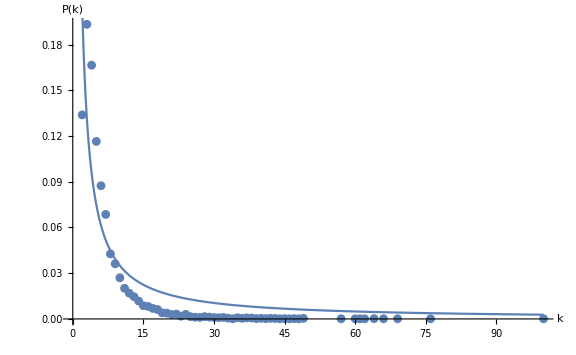

```mathematica
vis14=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igv14]//Mean//N
```

6.24982

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks=horizontalVisibility[series];
```

## Graph

```mathematica
igh14=Graph[horLinks, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh14];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→3571,5→931,3→2350,9→159,4→1505,7→376,6→579,12→48,10→96,8→237,13→28,14→14,11→79,15→12,16→1,18→5,17→4,19→1,24→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,3571/9999},{5,931/9999},{3,2350/9999},{9,53/3333},{4,1505/9999},{7,376/9999},{6,193/3333},{12,16/3333},{10,32/3333},{8,79/3333},{13,28/9999},{14,14/9999},{11,79/9999},{15,4/3333},{16,1/9999},{18,5/9999},{17,4/9999},{19,1/9999},{24,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.19285/x^1.653]

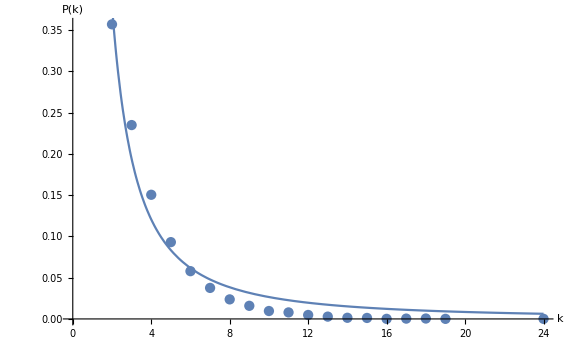

```mathematica
hvis11=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igh14]//Mean//N
```

3.76678

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,14,9999,6.24982,1.09851 ± 0.181382,0.438859 ± 0.113674},{horizontal,14,9999,3.76678,1.653 ± 0.214014,1.19285 ± 0.253044}}